Function[{f$},Norm[f$[tmax]-{0,0}]≤tol]

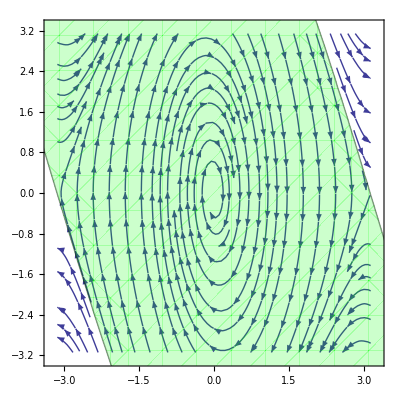

```mathematica
tmax=40;
tol=0.2;

(*Solution to ODE that maps t to {x[t],y[t]}*)
sol[x0_?NumericQ,y0_?NumericQ]:=First@NDSolve[{x[0]==x0,y[0]==y0,x'[t]==y[t],y'[t]==-9 Sin[x[t]]-0.5 y[t]+Cos[10*t]},{x,y},{t,0,tmax}]/.HoldPattern[{x->xi_,y->yi_}]:>Function[{t},{xi[t],yi[t]}];

(*Create function that takes a solution as argument and checks if it's close to attractor at tmax*)
MakeBasinTest[{x0_,y0_}]:=Function[{f},Norm[f[tmax]-{x0,y0}]≤tol];

inCenterBasinQ=MakeBasinTest[{0,0}]

(*Create streamplot and basin region,give it a while*)
(*Show[StreamPlot[{y,-9 Sin[x]-0.2 y},{x,-10,10},{y,-10,10}],RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,-10,10},{y0,-10,10},PlotPoints->30,MaxRecursion->1,PlotStyle->{Green,Opacity[0.2]}]]*)
Show[StreamPlot[{y,-9 Sin[x]-0.5 y},{x,-Pi,Pi},{y,-Pi,Pi}],RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,-10,10},{y0,-10,10},PlotPoints->30,MaxRecursion->1,PlotStyle->{Green,Opacity[0.2]}]]
```

```mathematica
ClearSystemCache;
```

Function[{f$},Norm[f$[tmax]-{0,0}]≤tol]

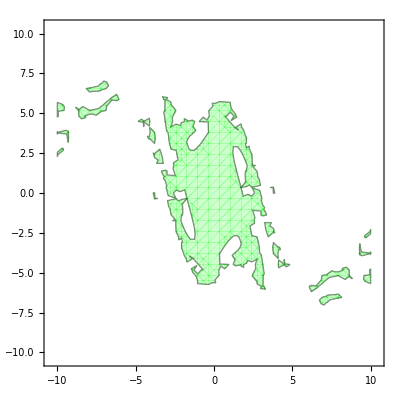

```mathematica
tmax=40;
tol=0.2;

(*Solution to ODE that maps t to {x[t],y[t]}*)
sol[x0_?NumericQ,y0_?NumericQ]:=First@NDSolve[{x[0]==x0,y[0]==y0,x'[t]==y[t],y'[t]==-9 Sin[x[t]]*(1+Cos[10*t])-0.2 y[t]},{x,y},{t,0,tmax}]/.HoldPattern[{x->xi_,y->yi_}]:>Function[{t},{xi[t],yi[t]}];

(*Create function that takes a solution as argument and checks if it's close to attractor at tmax*)
MakeBasinTest[{x0_,y0_}]:=Function[{f},Norm[f[tmax]-{x0,y0}]≤tol];

inCenterBasinQ=MakeBasinTest[{0,0}]

(*Create streamplot and basin region,give it a while*)
Show[StreamPlot[{y,-9 Sin[x]*(1+Cos[10*t])-0.2 y},{x,-10,10},{y,-10,10}],RegionPlot[inCenterBasinQ[sol[x0,y0]],{x0,-10,10},{y0,-10,10},PlotPoints->30,MaxRecursion->1,PlotStyle->{Green,Opacity[0.2]}]]
```

```mathematica
ClearSystemCache;

DuffingForced={x'[t]==y[t],y'[t]==x[t]-x[t]^3-0.25 y[t]+0.25 Cos[t]};
```

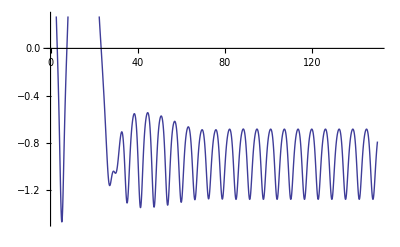

```mathematica
Plot[Evaluate[x[t]/.First[NDSolve[{DuffingForced,x[0]==1,y[0]==1.1},{x[t],y[t]},{t,0,150}]]],{t,0,150}]
tmax=8*Pi;
```

```mathematica
AttractingWell[a_,b_]:=Sign[x[t]]/.First[NDSolve[{DuffingForced,x[0]==a,y[0]==b},{x[t],y[t]},{t,0,tmax}]]/.t->tmax;
```

```mathematica
DensityPlot[AttractingWell[a,b],{a,-2.5,2.5},{b,-2.5,2.5},PlotPoints->130,MaxRecursion->3,Mesh->False,ColorFunction->(If[# ≠ 1,Blue,Yellow] &), FrameTicks->{Range[-2,2],Range[-2,2],None,None}]
```

-Graphics-